```mathematica
(*Construcción de funciones de onda espinoriales-Versión Filtrada (6 términos)*)ClearAll["Global`*"];

(*1. Configuración de símbolos y asunciones*)
energias={en,en1,en2,en3,en4};
angulos={th,th1,th2,th3,th4,ph,ph1,ph2,ph3,ph4,zet};
asunciones=Join[Thread[energias>0],{Element[angulos,Reals],g>0,mphi>=0}];
$Assumptions=Element[{th,ph},Reals]&&(lambda==1/2||lambda==-1/2);

procesar[expr_]:=FullSimplify[ComplexExpand[expr],asunciones];

(*Definiciones espinoriales*)
chi[1/2,th_,ph_]:={{Exp[-I ph/2] Cos[th/2]},{Exp[I ph/2] Sin[th/2]}};
chi[-1/2,th_,ph_]:={{-Exp[-I ph/2] Sin[th/2]},{Exp[I ph/2] Cos[th/2]}};
omega[lambda_,en_]:=Sqrt[en+2 lambda en];

xAlphaDown[en_,lambda_,th_,ph_]:=omega[-lambda,en]*chi[lambda,th,ph];
xAlphaUp[en_,lambda_,th_,ph_]:=-2 lambda*omega[-lambda,en]*procesar[ConjugateTranspose[chi[-lambda,th,ph]]];
yAlphaDown[en_,lambda_,th_,ph_]:=2 lambda*omega[lambda,en]*chi[-lambda,th,ph];
yAlphaUp[en_,lambda_,th_,ph_]:=omega[lambda,en]*procesar[ConjugateTranspose[chi[lambda,th,ph]]];
xDaggerAlphaUp[en_,lambda_,th_,ph_]:=-2 lambda*omega[-lambda,en]*chi[-lambda,th,ph];
xDaggerAlphaDown[en_,lambda_,th_,ph_]:=omega[-lambda,en]*procesar[ConjugateTranspose[chi[lambda,th,ph]]];
yDaggerAlphaUp[en_,lambda_,th_,ph_]:=omega[lambda,en]*chi[lambda,th,ph];
yDaggerAlphaDown[en_,lambda_,th_,ph_]:=2 lambda*omega[lambda,en]*procesar[ConjugateTranspose[chi[-lambda,th,ph]]];

(*Parámetros físicos y cinemática*)
reglasCinematica={en1->en,en2->en,en3->en,en4->en,th1->0,ph1->0,th2->Pi,ph2->Pi,th3->th,ph3->ph,th4->Pi-th,ph4->Pi+ph};
parRound[aUp_,bDown_]:=(aUp.bDown)[[1,1]];
parSquare[aDownStar_,bUpStar_]:=(aDownStar.bUpStar)[[1,1]];

reglasMandelstam={s->4*en^2,t->-2*en^2*(1-Cos[th]),u->-2*en^2*(1+Cos[th])};
simplificacionesExtra={1-Cos[th]->2*Sin[th/2]^2,1+Cos[th]->2*Cos[th/2]^2};
```

```mathematica
(*2. Función modificada para obtener solo los 6 términos (3 y 4 de cada canal)*)
calcularBloques[h1_,h2_,h3_,h4_]:=Module[{s3l,s4l,t3l,t4l,u3l,u4l,lista,reglasLocales},reglasLocales=Join[reglasCinematica,{lambdaC->g}];
(*Solo se calculan los bloques requeridos*)s3l=lambdaC^2*parRound[xAlphaUp[en1,h1,th1,ph1],xAlphaDown[en2,h2,th2,ph2]]*parSquare[xDaggerAlphaDown[en3,h3,th3,ph3],xDaggerAlphaUp[en4,h4,th4,ph4]];
s4l=lambdaC^2*parSquare[yDaggerAlphaDown[en1,h1,th1,ph1],yDaggerAlphaUp[en2,h2,th2,ph2]]*parRound[yAlphaUp[en3,h3,th3,ph3],yAlphaDown[en4,h4,th4,ph4]];
t3l=lambdaC^2*parSquare[xDaggerAlphaDown[en3,h3,th3,ph3],yDaggerAlphaUp[en1,h1,th1,ph1]]*parRound[yAlphaUp[en4,h4,th4,ph4],xAlphaDown[en2,h2,th2,ph2]];
t4l=lambdaC^2*parRound[yAlphaUp[en3,h3,th3,ph3],xAlphaDown[en1,h1,th1,ph1]]*parSquare[xDaggerAlphaDown[en4,h4,th4,ph4],yDaggerAlphaUp[en2,h2,th2,ph2]];
u3l=lambdaC^2*parSquare[xDaggerAlphaDown[en4,h4,th4,ph4],yDaggerAlphaUp[en1,h1,th1,ph1]]*parRound[yAlphaUp[en3,h3,th3,ph3],xAlphaDown[en2,h2,th2,ph2]];
u4l=lambdaC^2*parRound[yAlphaUp[en4,h4,th4,ph4],xAlphaDown[en1,h1,th1,ph1]]*parSquare[xDaggerAlphaDown[en3,h3,th3,ph3],yDaggerAlphaUp[en2,h2,th2,ph2]];
(*Lista filtrada:s3,s4,t3,t4,u3,u4*)lista={(I/(s-mphi^2))*s3l,(I/(s-mphi^2))*s4l,(-I/(t-mphi^2))*t3l,(-I/(t-mphi^2))*t4l,(I/(u-mphi^2))*u3l,(I/(u-mphi^2))*u4l}/. reglasLocales;
Map[procesar[#/. reglasMandelstam/. simplificacionesExtra/. mphi->valorMasa]&,lista]];

(*3. Ejecución*)
l1=+1/2;l2=-1/2;
valorMasa=m;

configSalida={{1/2,1/2,"++"},{-1/2,-1/2,"--"},{1/2,-1/2,"+-"},{-1/2,1/2,"-+"}};
cabecera={"h3 h4","S3","S4","T3","T4","U3","U4","Total iM"};

filasTabla=Table[With[{h3=c[[1]],h4=c[[2]],label=c[[3]]},bloques=calcularBloques[l1,l2,h3,h4];
total=Total[bloques];
Join[{label},bloques,{total}]],{c,configSalida}];

(*4. Resultados y Concurrencia*)
{MRR,MLL,MRL,MLR}=filasTabla[[All,-1]];
NormN=procesar[Sqrt[Abs[MRR]^2+Abs[MLL]^2+Abs[MRL]^2+Abs[MLR]^2]];
{CRR,CLL,CRL,CLR}={MRR,MLL,MRL,MLR}/NormN;
Delta=procesar[2*Abs[CRR*CLL-CRL*CLR]];
(*Sustitución de theta=Pi/2 en Delta*)
deltaPiMedios=procesar[Delta/. th->Pi/2];
Print["Delta (th = Pi/2): ",deltaPiMedios];
limitemasa0=Limit[Delta, valorMasa->0]
Print["--- AMPLITUDES POR HELICIDAD DE SALIDA (m_phi = 0) ---"];
Print["--- DESGLOSE DE CONTRIBUCIONES POR CONFIGURACIÓN (M = ",valorMasa,") ---"];
Print[Grid[Prepend[filasTabla,cabecera],Frame->All,Background->{None,{Lighter[Gray,0.9],None}}]];
Print["M[i;++] = ",FullSimplify[MRR]];
Print["M[i;--] = ",FullSimplify[MLL]];
Print["M[i;+-] = ",FullSimplify[MRL]];
Print["M[i;-+] = ",FullSimplify[MLR]];
Print["N (normalización) = ",FullSimplify[NormN]];
Print["--- CONCURRENCIA ---"];
Print["Concurrencia = ",FullSimplify[Delta]];
Print["Concurrencia para límite masa nula = ", FullSimplify[limitemasa0]]

Print["--- DESGLOSE DE CONTRIBUCIONES FILTRADAS (S3, S4, T3, T4, U3, U4) ---"];
Print[Grid[Prepend[filasTabla,cabecera],Frame->All,Background->{None,{Lighter[Gray,0.9],None}}]];
Print["Concurrencia = ",FullSimplify[Delta]];
```

Delta (th = Pi/2): 1

-(8 √(en^4 (-1+Cos[th])^2) (1+Cos[th]) Sin[th]^2)/(√(en^4) (-3+4 Cos[2 th]-Cos[4 th]))

--- AMPLITUDES POR HELICIDAD DE SALIDA (m_phi = 0) ---

--- DESGLOSE DE CONTRIBUCIONES POR CONFIGURACIÓN (M = m) ---

h3 h4 | S3 | S4 | T3 | T4 | U3 | U4 | Total iM
++ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-- | 0 | 0 | 0 | 0 | 0 | 0 | 0
+- | 0 | 0 | 0 | 0 | (4 en^2 g^2 Cos[th/2]^2 (-ⅈ Cos[ph]+Sin[ph]))/(2 en^2+m^2+2 en^2 Cos[th]) | 0 | (4 en^2 g^2 Cos[th/2]^2 (-ⅈ Cos[ph]+Sin[ph]))/(2 en^2+m^2+2 en^2 Cos[th])
-+ | 0 | 0 | (4 ⅈ ⅇ^(ⅈ ph) en^2 g^2 Sin[th/2]^2)/(2 en^2+m^2-2 en^2 Cos[th]) | 0 | 0 | 0 | (4 ⅈ ⅇ^(ⅈ ph) en^2 g^2 Sin[th/2]^2)/(2 en^2+m^2-2 en^2 Cos[th])

M[i;++] = 0

M[i;--] = 0

M[i;+-] = (4 en^2 g^2 Cos[th/2]^2 (-ⅈ Cos[ph]+Sin[ph]))/(2 en^2+m^2+2 en^2 Cos[th])

M[i;-+] = (4 ⅈ ⅇ^(ⅈ ph) en^2 g^2 Sin[th/2]^2)/(2 en^2+m^2-2 en^2 Cos[th])

N (normalización) = 4 en^2 g^2 √(Cos[th/2]^4/((2 en^2+m^2+2 en^2 Cos[th])^2)+Sin[th/2]^4/((2 en^2+m^2-2 en^2 Cos[th])^2))

--- CONCURRENCIA ---

Concurrencia = (2 √((2 en^2+m^2-2 en^2 Cos[th])^2) √((2 en^2+m^2+2 en^2 Cos[th])^2) Sin[th]^2)/(3 en^4+4 en^2 m^2+3 m^4+(-4 en^4-4 en^2 m^2+m^4) Cos[2 th]+en^4 Cos[4 th])

Concurrencia para límite masa nula = 1

--- DESGLOSE DE CONTRIBUCIONES FILTRADAS (S3, S4, T3, T4, U3, U4) ---

h3 h4 | S3 | S4 | T3 | T4 | U3 | U4 | Total iM
++ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-- | 0 | 0 | 0 | 0 | 0 | 0 | 0
+- | 0 | 0 | 0 | 0 | (4 en^2 g^2 Cos[th/2]^2 (-ⅈ Cos[ph]+Sin[ph]))/(2 en^2+m^2+2 en^2 Cos[th]) | 0 | (4 en^2 g^2 Cos[th/2]^2 (-ⅈ Cos[ph]+Sin[ph]))/(2 en^2+m^2+2 en^2 Cos[th])
-+ | 0 | 0 | (4 ⅈ ⅇ^(ⅈ ph) en^2 g^2 Sin[th/2]^2)/(2 en^2+m^2-2 en^2 Cos[th]) | 0 | 0 | 0 | (4 ⅈ ⅇ^(ⅈ ph) en^2 g^2 Sin[th/2]^2)/(2 en^2+m^2-2 en^2 Cos[th])

Concurrencia = (2 √((2 en^2+m^2-2 en^2 Cos[th])^2) √((2 en^2+m^2+2 en^2 Cos[th])^2) Sin[th]^2)/(3 en^4+4 en^2 m^2+3 m^4+(-4 en^4-4 en^2 m^2+m^4) Cos[2 th]+en^4 Cos[4 th])

```mathematica
Print[FullSimplify[Delta /.{th->Pi/2}]]
```

1

```mathematica
(*VISUALIZACIÓN CON X*)
asuncionesAmpliadas={m>0,Element[{x,th},Reals]};
Deltax=FullSimplify[Delta/. {en->m*x}];
Deltaxsimplify=FullSimplify[Deltax,Assumptions->asuncionesAmpliadas]
Print["Delta(x)= ",Deltaxsimplify]
```

1-(4 Cos[th]^2)/(3+4 x^2+3 x^4+(1-4 (x^2+x^4)) Cos[2 th]+x^4 Cos[4 th])

Delta(x)= 1-(4 Cos[th]^2)/(3+4 x^2+3 x^4+(1-4 (x^2+x^4)) Cos[2 th]+x^4 Cos[4 th])

```mathematica
(*Visualización dinámica conectada directamente a la variable calculada*)Manipulate[Plot[(*Evaluate fuerza a Mathematica a leer el contenido de Deltaxsimplify.La regla de sustitución (/. {x->varX,th->varTh}) inyecta los valores del slider y del eje X en tu expresión global.*)Evaluate[Deltaxsimplify/. {x->varX,th->varTh}],{varTh,0,Pi},PlotRange->{{0,Pi},{0,1.05}},Frame->True,FrameLabel->{"θ (rad)","Δ"},PlotStyle->{Medium,Blue},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12},Exclusions->None],(*El slider controla la variable local varX*){{varX,1,"Parámetro x = E/m"},0,10,Appearance->"Labeled"}]
```

```mathematica
(*GENERACIÓN DE PDFS*)
SetDirectory[NotebookDirectory[]];
(*1. Definición de la lista de valores de x solicitados*)valoresX={0.001,0.01,0.1,0.67,1,2,10,100,1000};
(*1. Grosor y estilo general de las líneas de los ejes*)estiloLíneasAjes=Directive[Medium,Opacity[0.8]];

(*2. Función detallada para el eje Y (sin ScientificForm)*)
yTicksConMinimos[ymin_,ymax_]:=Module[{ticksY,ticksYMinimos},(*Se utiliza'y' directamente como etiqueta en lugar de ScientificForm*)ticksY=Table[{y,y,{0.025,0}},{y,0.2,1.0,0.2}];
ticksYMinimos=Table[{y,"",{0.0125,0}},{y,0.0,1.0,0.04}];
Join[ticksY,ticksYMinimos]];

(*3. Función detallada para el eje X hasta Pi*)
xTicksConMinimos[xmin_,xmax_]:=Module[{ticksX,ticksXMinimos},(*Ticks principales etiquetados en los números enteros:1,2,3*)ticksX=Table[{x,x,{0.025,0}},{x,1,Floor[Pi],1}];
(*Ticks menores sin etiqueta con un paso de 0.25 (4 divisiones por unidad)*)ticksXMinimos=Table[{x,"",{0.0125,0}},{x,0,Pi,0.25}];
Join[ticksX,ticksXMinimos]];

(*4. Consolidación del estilo detallado*)
estiloAjesDetallado={Ticks->{xTicksConMinimos,yTicksConMinimos},AxesStyle->estiloLíneasAjes,TicksStyle->Directive[FontFamily->"Helvetica",FontSize->18,Medium,Opacity[0.8]],AxesLabel->{Style["θ",20],Style["Δ",20]},PlotStyle->{ColorData[97,1]},PlotRange->{{0,Pi},{0,1.05}},LabelStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,AspectRatio->1/GoldenRatio};

(*3. Bucle de generación y exportación de PDFs*)
Do[Module[{grafica,nombreArchivo},(*Sustituimos el valor de x en tu expresión analítica*)grafica=Plot[Evaluate[Deltaxsimplify/. x->val],{th,0,Pi},(*Ajustado a 2Pi según el eje de tu imagen*)Evaluate[estiloAjesDetallado]];
(*Creamos un nombre de archivo limpio*)nombreArchivo="Concurrencia_para_x="<>ToString[val]<>".pdf";
(*Exportación*)Export[nombreArchivo,grafica];
Print["Exportado: ",nombreArchivo];],{val,valoresX}]
```

Exportado: Concurrencia_para_x=0.001.pdf

Exportado: Concurrencia_para_x=0.01.pdf

Exportado: Concurrencia_para_x=0.1.pdf

Exportado: Concurrencia_para_x=0.67.pdf

Exportado: Concurrencia_para_x=1.pdf

Exportado: Concurrencia_para_x=2.pdf

Exportado: Concurrencia_para_x=10.pdf

Exportado: Concurrencia_para_x=100.pdf

Exportado: Concurrencia_para_x=1000.pdf

```mathematica
(*AHORA HAGO EL TAYLOR*)
(*1. Desarrollo en serie de Taylor alrededor de x=0 hasta orden 4*)serieDelta=Series[Deltaxsimplify,{x,0,4}];

(*2. Truncamiento del término de error O[x]^5 para obtener una expresión algebraica*)
serieNormal=Normal[serieDelta];

(*3. Simplificación rigurosa asumiendo ángulos reales*)
serieSimplificada=FullSimplify[serieNormal,Assumptions->{Element[th,Reals]}];

(*4. Visualización del resultado ordenado por potencias de x*)
Print["Desarrollo de Taylor de Δ(x, θ) en x=0:"];
Print[Collect[serieSimplificada,x,FullSimplify]];
```

Desarrollo de Taylor de Δ(x, θ) en x=0:

-1+4/(3+Cos[2 th])+(8 x^2 Sin[2 th]^2)/(3+Cos[2 th])^2

Desarrollo de Taylor de Δ(x, θ) en x=0:

-1+4/(3+Cos[2 th])+(8 x^2 Sin[2 th]^2)/(3+Cos[2 th])^2

Desarrollo de Taylor de Δ(x, θ) en x=0:

-1+4/(3+Cos[2 th])+(32 x^4 Cos[th]^2 (-5+Cos[2 th]) Sin[th]^4)/(3+Cos[2 th])^3+(8 x^2 Sin[2 th]^2)/(3+Cos[2 th])^2

-1+4/(3+Cos[2 th])

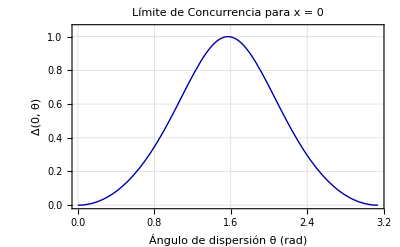

```mathematica
(*1. Definición de la función límite a orden 0*)
DeltaOrdenCero[th_]:=Sin[th]^2/(1+Cos[th]^2);
(*2. Visualización con el estilo estandarizado*)
Plot[DeltaOrdenCero[th],{th,0,Pi},PlotRange->{{0,Pi},{0,1.05}},Frame->True,FrameLabel->{"Ángulo de dispersión θ (rad)","Δ(0, θ)"},PlotStyle->{Thick,Darker[Blue]},GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14},PlotLabel->Style["Límite de Concurrencia para x = 0",14]]
```

```mathematica
(*VISUALIZACIÓN CON Y*)
asuncionesAmpliadas={en>0,Element[{y,th},Reals]};
Deltay=FullSimplify[Delta/. {m->en*y}];
Deltaysimplify=FullSimplify[Deltay,Assumptions->asuncionesAmpliadas]
Print["Delta(y)= ",Deltaysimplify]
```

(2 ((2+y^2)^2-4 Cos[th]^2) Sin[th]^2)/(3+4 y^2+3 y^4+(-4-4 y^2+y^4) Cos[2 th]+Cos[4 th])

Delta(y)= (2 ((2+y^2)^2-4 Cos[th]^2) Sin[th]^2)/(3+4 y^2+3 y^4+(-4-4 y^2+y^4) Cos[2 th]+Cos[4 th])

```mathematica
(*1. Desarrollo en serie de Taylor alrededor de x=0 hasta orden 4*)serieDeltay=Series[Deltaysimplify,{y,0,8}];

(*2. Truncamiento del término de error O[x]^5 para obtener una expresión algebraica*)
serieNormaly=Normal[serieDeltay];

(*3. Simplificación rigurosa asumiendo ángulos reales*)
serieSimplificaday=FullSimplify[serieNormaly,Assumptions->{Element[th,Reals]}];

(*4. Visualización del resultado ordenado por potencias de x*)
Print["Desarrollo de Taylor de Δ(x, θ) en x=0:"];
Print[Collect[serieSimplificaday,y,FullSimplify]]
```

Desarrollo de Taylor de Δ(x, θ) en x=0:

1-1/2 y^4 Cot[th]^2 Csc[th]^2+1/2 y^6 Cot[th]^2 Csc[th]^4+1/16 y^8 (-5+Cos[2 th]) Cot[th]^2 Csc[th]^6